# 5.3 Renyi dimension of Hénon map

## The Hénon map is defined by the following recursion Iterating an initial condition using the Hénon map leads to a solution in the form of a sequence of points in the plane (an orbit): . Just as for continuous dynamical systems, a discrete dynamical system may have a strange attractor, but it can be of lower dimension than for continuous systems. This makes it easier to analyze its fractal dimension. Your task is to explore the Hénon map for the values and .

## a) Plot an approximation of the fractal attractor by iterating the Hénon map a large number of times for different initial positions. You may discard the initial transient as it is expected to lie too far from the attractor.

```mathematica
ClearAll["Global`"]
a = 1.4;
b = 0.3;
data1 = Drop[NestList[{#[[2]] + 1 - a*#[[1]]^2, b*#[[1]]} &, {0.1, 0.1}, 100000], 4];
data2 = Drop[NestList[{#[[2]] + 1 - a*#[[1]]^2, b*#[[1]]} &, {1, 1}, 100000], 4];
data3 = Drop[NestList[{#[[2]] + 1 - a*#[[1]]^2, b*#[[1]]} &, {1.1, 1.1}, 100000], 4];

Plot1 = ListPlot[data1, PlotLabel -> "Initial Starting Point: {0.1, 0.1}"];
Plot2 = ListPlot[data2, PlotLabel -> "Initial Starting Point: {1, 1}"];
Plot3 = ListPlot[data3, PlotLabel -> "Initial Starting Point: {1.1, 1.1}"];
```

## In the following exercises you are going to compute the fractal dimension spectrum ​​ for the Hénon attractor. You may find the following hints helpful: 1) Recall that is a non-increasing function of , which means that if . 2) If then attains the limit . 3) If you are using Mathematica, you may want to use the function BinCounts[] to bin your data. Using data points with bin sizes ranging from to ​​ gives good results.

## b) Make three plots against in the range of ϵ stated in the hints above. The first two plots show for and and the last plot shows . You should see a linear slope in these three plots.

1.23289

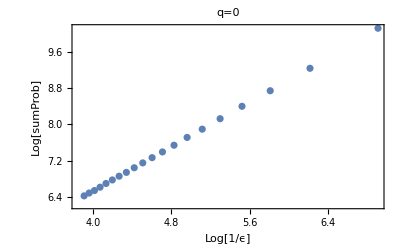

```mathematica
ClearAll["Global`*"]
a = 1.4;
b = 0.3;
q = 0.;

data = Drop[NestList[{#[[2]]+1-a*#[[1]]^2,b*#[[1]]} &, {0.1,0.1}, 2*10^6-1]];
bins = Table[Flatten[BinCounts[data, ϵ, ϵ]], {ϵ,0.001,0.02,0.001}];
NBoxes = Table[2*10^6-1,{i,Length[bins]}];
probabilities = Table[Select[Divide[bins[[i]],NBoxes[[i]]],#>0.&],{i,Length[bins]}];

sumProb = Table[Sum[p^q,{p, probabilities[[i]]}],{i,Length[bins]}];

yValues = Table[Divide[Log[sumProb[[i]]],(1-q)],{i,Length[bins]}];
xValues = Log[1/Range[0.001,0.02,0.001]];

nominator = Last[yValues]-First[yValues];
denominator = Last[xValues]-First[xValues];
slope = nominator/denominator

ListPlot[Transpose[{xValues, yValues}], Frame -> True, 
 FrameLabel -> {"Log[1/ϵ]", "Log[sumProb]"}, 
 PlotLabel -> "q=0"]
```

1.22716

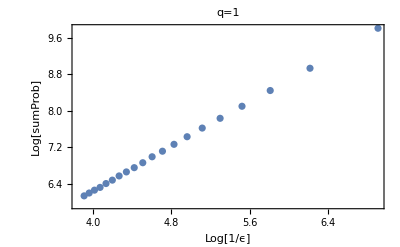

```mathematica
ClearAll["Global`*"]
a = 1.4;
b = 0.3;
q = 1.;

data = Drop[NestList[{#[[2]] + 1 - a*#[[1]]^2, b*#[[1]]} &, {0.1, 0.1}, 2*10^6 - 1]];

bins = Table[Flatten[BinCounts[data, ϵ, ϵ]], {ϵ, 0.001, 0.02, 0.001}];
NBoxes = Table[2*10^6-1,{i,Length[bins]}];

probabilities = Table[Select[Divide[bins[[i]], NBoxes[[i]]], # > 0. &], {i,Length[bins]}];

sumProb = Table[Sum[Times[p,Log[1/p]], {p, probabilities[[i]]}], {i,Length[bins]}];

yValues = Table[sumProb[[i]], {i,Length[bins]}];
xValues = Log[1/Range[0.001,0.02,0.001]];

nominator = Last[yValues]-First[yValues];
denominator = Last[xValues]-First[xValues];
slope = nominator/denominator

ListPlot[Transpose[{xValues, yValues}], Frame -> True, PlotRange->Full,
 FrameLabel -> {"Log[1/ϵ]", "Log[sumProb]"},
 PlotLabel -> "q=1"]
```

1.18521

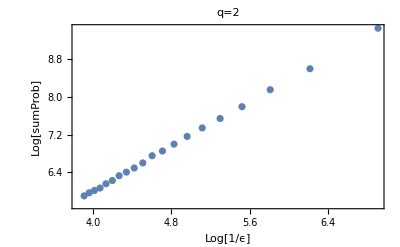

```mathematica
ClearAll["Global`*"]
a = 1.4;
b = 0.3;
q = 2;

data = Drop[NestList[{#[[2]]+1-a*#[[1]]^2,b*#[[1]]} &, {0.1,0.1}, 2*10^6-1]];
bins = Table[Flatten[BinCounts[data, ϵ, ϵ]], {ϵ,0.001,0.02,0.001}];

NBoxes = Table[2*10^6-1,{i,Length[bins]}];
Select[Divide[bins[[1]],NBoxes[[1]]],#>0&];

probabilities = Table[Select[Divide[bins[[i]],NBoxes[[i]]],#>0&],{i,Length[bins]}];

sumProb = Table[Sum[p^q,{p, probabilities[[i]]}],{i,Length[bins]}];

yValues = Table[Divide[Log[sumProb[[i]]],(1-q)],{i,Length[bins]}];
xValues = Log[1/Range[0.001,0.02,0.001]];

nominator = Last[yValues]-First[yValues];
denominator = Last[xValues]-First[xValues];
slope = nominator/denominator

ListPlot[Transpose[{xValues, yValues}], Frame -> True, 
 FrameLabel -> {"Log[1/ϵ]", "Log[sumProb]"}, 
 PlotLabel -> "q=2"]
```

## c) Using the plots made in (b) compute estimates for (box-counting dimension), (information dimension) and (correlation dimension) of the Hénon attractor. Give your result as the vector with two decimal digits of accuracy.

[1.23289, 1.22716, 1.18521]

## d) Make a graph of as a function of , for with at least 9 different values of . Your plot should confirm that is non-increasing (up to potential small deviations due to finite resolution ϵ).

```mathematica
ClearAll["Global`*"]
a = 1.4;
b = 0.3;
IterationSteps = 2*10^6-1;
DQ = ParallelTable[
  data = Drop[NestList[{#[[2]] + 1 - a*#[[1]]^2, b*#[[1]]} &, {0.1, 0.1}, IterationSteps]];
  bins = Table[Flatten[BinCounts[data, ϵ, ϵ]], {ϵ, 0.001, 0.02, 0.001}];
  NBoxes = Table[IterationSteps,{i,Length[bins]}];
  probabilities = Table[Select[Divide[bins[[i]], NBoxes[[i]]], # > 0. &], {i, Length[bins]}];
  
  sumProb = Table[Sum[p^q, {p, probabilities[[i]]}], {i, Length[bins]}];

  yValues = Table[Divide[Log[sumProb[[i]]], (1 - q)], {i, Length[bins]}];
  xValues = Log[1/Range[0.001,0.02,0.001]];
  
  nominator = Last[yValues] - First[yValues];
  denominator = Last[xValues] - First[xValues];
  slope = nominator/denominator;
  slope,
  {q, Subdivide[0., 4., 9.]}
]

ListPlot[Transpose[{Subdivide[0, 4, 9], DQ}], Frame -> True, 
FrameLabel -> {"q", ""}, PlotLabel -> " as a function of "]
```

{1.23289,1.23504,1.22944,1.21788,1.19857,1.16904,1.12819,1.07887,1.02765,0.980774}

## Now compute the Lyapunov exponents and ​​ for Hénon map. Hints: You can use the discrete version of the QR-decomposition procedure which is very similar to that used for the Lyapunov exponents of the Lorenz model. The dynamics in Eq. (1) is discrete, meaning you do not have to discretize the dynamics to compute the Stability matrix M: where J is the Jacobian of the right-hand side in Eq. (1). As a comparison, after the discretization of a continuous dynamical system we had . When computing the Lyapunov dimensions below, recall that the Kaplan-Yorke conjecture says that ​​ .

## e) Compute the Lyapunov exponents and numerically. Give your result as the ordered vector with with two decimal digits accuracy.

```mathematica
ClearAll["Global`*"]

a = 1.4;
b = 0.3;
tMax = 10000;

(*Generate Data*)
data = NestList[{#[[2]]+1-a*#[[1]]^2,b*#[[1]]} &, {1,1}, tMax];

(*Define the jacobian and it's value depending on data*)
jacFunc[x_] := {{-2*a*x, 1}, {b,0}};
jacobian = Table[jacFunc[x],{x,data[[All, 1]]}];

Qold = IdentityMatrix[2];
Mold = IdentityMatrix[2];
λ1 = 0;
λ2 = 0;
lambdaValues = ConstantArray[0, {tMax, 3}];
t = 1;
For[i = 1, i <= tMax, i++,
  Mold = jacobian[[i]];
  QRValues = QRDecomposition[Mold . Qold];
  Qold = Transpose[QRValues[[1]]];
  Rold = QRValues[[2]];
  λ1 += Log[Abs[Rold[[1, 1]]]];
  λ2 += Log[Abs[Rold[[2, 2]]]];
  lambdaValues[[t]] = {i, λ1/i, λ2/i};
  t++;
]

a= λ1/tMax;
b= λ2/tMax;
{a,b}
```

{0.41376,-1.61773}

## f) Using the Lyapunov exponents computed above, calculate the Lyapunov dimension . Give your result with two decimal digits accuracy.

```mathematica
DL = 1-a/b
```

1.25577